```mathematica
(*Berry curvature on a plaquette, with PBCs*)
(*z is a matrix ni*nj, with (i,j) element the eigenstate in the grid point (Subscript[k, x,i],Subscript[k, y,j]) *)
BerryCurvature[z_,i_,j_]:=Module[{γ,ni,nj,CompDot},
CompDot[a_,b_]:=Conjugate[a].b;
ni=Dimensions[z][[1]]; 
nj=Dimensions[z][[2]]; 
γ=CompDot[ z[[i,j]],z[[i ,Mod[j+1,nj,1]]] ];
γ= γ*CompDot[ z[[i,Mod[j+1,nj,1]]] ,z[[ Mod[i+1,ni,1] ,Mod[j+1,nj,1] ]] ];
γ= γ*CompDot[ z[[Mod[i+1,ni,1],Mod[j+1,nj,1]]],z[[Mod[i+1,ni,1],j]] ];
γ= γ*CompDot[ z[[Mod[i+1,ni,1],j]],z[[i,j]] ];
 Arg[γ]
]

(*Sum over the plaquettes*)
TotalBerryCurvature[z_]:=Module[{ni,nj},
ni=Dimensions[z][[1]];
nj=Dimensions[z][[2]];
Table[BerryCurvature[z,i,j](*/(2Pi)*),{i,1,ni},{j,1,nj}]
]
ChernNumber[z_]:=1/(2Pi)Chop[Sum[BerryCurvature[z,i,j],{i,1,Dimensions[z][[1]]},{j,1,Dimensions[z][[2]]}]]


(*Without - sign in front of H*)
ChernHamiltonian[α_,kx_,ky_]:=Module[{a,t,Q,Hmatrix},
a=1; (*Unit of length*)
t=1; (*Unit of energy*)
Q=If[α>0,Denominator[Rationalize[α]], 1];

Hmatrix  = SparseArray[
{
{i_,j_}/;Abs[i-j]==1 ->1,
{i_,j_}/;Abs[i-j]==0 ->2t Cos[ky a-2 Pi α i],
{1,Q} -> t Exp[I kx Q a],
{Q,1} -> t Exp[-I kx Q a]
}
,{Q,Q},0];
Hmatrix = Normal[Hmatrix];
Hmatrix
]


test[α_,ν_,n_]:=Module[{a,Q,Ncx,Ncy,Nax,Nay},
a=1; (*Unit of length*)
Q=If[α>0,Denominator[Rationalize[α]], 1];
Ncy=n;
Ncx=n;
Nax=Q n;
Nay=Ncy;
Table[Transpose[Sort[Transpose[Eigensystem[N[ChernHamiltonian[α,kx,ky]]]],#1[[1]]<#2[[1]]&]][[2,ν]]
,{kx,0,(2Pi)/a*1/Nax(Ncx-1),(2Pi)/a*1/Nax},{ky,0,(2Pi)/a*1/Nay(Nay-1),(2Pi)/a*1/Nay}]
]
```

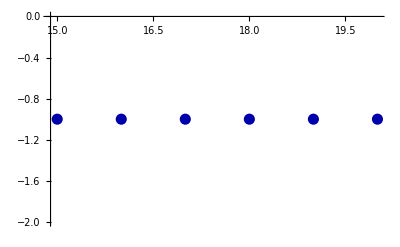

```mathematica
(*INPUT*)
alpha=3/4;
(*Band index, must be 1≤ν≤Q*)
nu=1;

p=ListPlot[Table[{n,ChernNumber[test[alpha,nu,n]]},{n,15,20}],PlotStyle->{Darker[Blue],PointSize[0.02]}]

(*Show[p,Axes->False,Frame->True,Frame->True, FrameLabel->{"m",C^nu},FrameTicks->{{ Automatic,None},{{1,2,3,4,5,6,7,8},None}}]*)
```

```mathematica
n=6;

Table[Chop[BerryCurvature[test[alpha,nu,n],i,j]],{i,1,Dimensions[test[alpha,nu,n]][[1]]},{j,1,Dimensions[test[alpha,nu,n]][[2]]}] // MatrixForm
```

(-0.0573289 | -0.0374572 | 0.0311563 | 0.526172 | 0.202606 | -0.017214
-0.00424052 | 0.00523719 | 0.0850519 | 0.61233 | 0.251923 | 0.0339719
0.0818157 | 0.0725699 | 0.172274 | 0.738926 | 0.326685 | 0.117116
0.0818157 | 0.0725699 | 0.172274 | 0.738926 | 0.326685 | 0.117116
-0.00424052 | 0.00523719 | 0.0850519 | 0.61233 | 0.251923 | 0.0339719
-0.0573289 | -0.0374572 | 0.0311563 | 0.526172 | 0.202606 | -0.017214)